```mathematica
(* MIT Sloan Data *)
```

```mathematica
path=NotebookDirectory[]
```

C:\Users\praha\Documents\Wolfram Mathematica\

```mathematica
dataset1 = SemanticImport[path<>"NexGen13newPlays.csv"]
```

Dataset[<>]

```mathematica
dataset1[All,#Distance&]
```

Dataset[<>]

```mathematica
dataset1[All,{5->(Quantity[#,"Feet"]&)}][All,{6->(Quantity[#,"Feet"]&)}][All,{7->(Quantity[#,"Feet"]&)}]
```

Dataset[<>]

```mathematica
datasetxy = dataset1[All,{2,3}]
```

Dataset[<>]

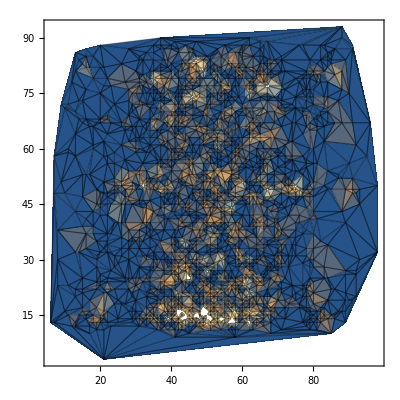

```mathematica
ListDensityPlot[Counts[Round[Normal@Values[datasetxy]/100]],Mesh->All]
```

```mathematica
datasetDistance= dataset1[All,{5,6}]
```

Dataset[<>]

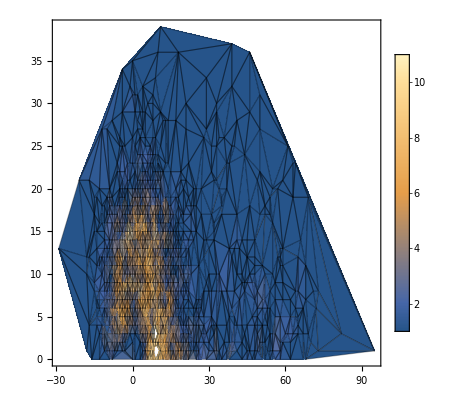

```mathematica
ListDensityPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],Mesh->All,PlotLegends->Automatic]
```